# Scalar decay into 2 fermions

```mathematica
$LoadPhi=True;
Needs["HighEnergyPhysics`FeynCalc`"];
```

Loading FeynCalc from /home/felipe/.Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading PHI

WARNING! Your FeynArts installation is not complete or the version you have cannot be used with this version of FeynCalc.
FeynArts can be downloaded at www.feynarts.de

Loading FeynArts, see www.feynarts.de for documentation

FeynArts not found. Please install FeynArts, e.g., in
/home/felipe/.Mathematica
and reload FeynCalc
FeynArts can be downloaded from www.feynarts.de

## Definiciones

```mathematica
$Assumptions =κ>0
dm[mu_]:=DiracMatrix[mu]     (*  Matriz de Dirac  *)
dm[5]:=DiracMatrix[5]             (*  Matriz Chiral gamma5  *)
ds[p_]:=DiracSlash[p]            (*  p^μ Subscript[γ, μ]  *)
mt[mu_,nu_]:=MetricTensor[mu,nu]       (*  Metrica  *)
fv[p_,mu_]:=FourVector[p,mu]           (*  4-vector p^μ  *)
sp[p_,q_]:=ScalarProduct[p,q]          (*  Producto escalar entre 4-vectores  *)
propu[p_,m_]:=ds[p]+m      (*  Numerador de propagador interno  *)
propv[p_,m_]:=ds[p]-m      (*  Numerador de propagador interno  *)
sigma[mu_,nu_]:=ⅈ/2 (dm[mu].dm[nu]-dm[nu].dm[mu])
R:=p1 + p2-q
IM:=IdentityMatrix[4]
```

κ>0

## Contribución escalar genérico

### Corriente generica

```mathematica
$Assumptions:=S∈Reals
$Assumptions:=P∈Reals
```

```mathematica
J1:=(Subscript[y, s]^f*S+ⅈ*Subscript[y, p]^f*P*dm[5])
J2:=(Subscript[y, s]^f S+ⅈ*Subscript[y, p]^f*P*dm[5])
```

#### Traza

```mathematica
T1:=propu[p1,mf].J1.propv[p2,mf].J2
Tra:=Simplify[Contract[Tr[T1]]];
ans=Simplify[Tra]
```

4 (P^2 y_p^(2 f) (p_1·p_2+mf^2)-S^2 y_s^(2 f) (mf^2-p_1·p_2))

#### Matriz M a nivel de arbol

```mathematica
Print["\!\(\*FractionBox[\(1\), \(4\)]\) \!\(\*UnderscriptBox[\(∑\), \(spins\)]\)|M\!\(\*SuperscriptBox[\(|\), \(2\)]\) = ",ans]
```

1/4 ∑_spins |M|^2 = 4 (P^2 (mf^2+p_1·p_2) y_p^(2 f)-S^2 (mf^2-p_1·p_2) y_s^(2 f))

#### Consideraciones cinematicas

```mathematica
kin1:={sp[p1,p2]->Mϕ^2/2*(1-(2*mf^2)/Mϕ^2),sp[p1,p1]->mf^2,sp[p2,p2]->mf^2} (*,sp[k,p1]->Mh^2/2,sp[k,p2]->Mh^2/2,sp[k,k]->Mh^2} *)
MM=FullSimplify[ans/.kin1]
```

2 S^2 (Mϕ^2-4 mf^2) y_s^(2 f)+2 Mϕ^2 P^2 y_p^(2 f)

#### Ancho de decaimiento (tree level)

```mathematica
final:=FullSimplify[N*(4*π)/(32*π^2)*MM*Mϕ/2*√(1-(4*mf^2)/Mϕ^2)*1/Mϕ^2]
Print["Γ(ϕ->f,f)=",final]
```

Γ(ϕ->f,f)=(√(1-(4 mf^2)/Mϕ^2) N (Mϕ^2 P^2 y_p^(2 f)+(Mϕ^2-4 mf^2) S^2 y_s^(2 f)))/(8 Mϕ π)

## Contribucion 4 fermiones

### Perturbamos los factores de forma

```mathematica
pert:={S->S+δS,P->P+δP}
```

```mathematica
Expfin=FullSimplify[Normal[Series[final/.pert,{S,0,1},{P,0,1}]]/.{δS^2->0,δP^2->0}]
```

(N √(1-(4 mf^2)/Mϕ^2) (δS S (Mϕ^2-4 mf^2) y_s^(2 f)+δP Mϕ^2 P y_p^(2 f)))/(4 π Mϕ)

## Corrientes Vector-Axial

```mathematica
JA[mu_]:=√(3/(16*Λ^2))* dm[mu].dm[5]
```

### Canal S

```mathematica
numAs=FullSimplify[ Contract[ JA[mu].propu[R,mf].(Subscript[y, s]^f*S+ⅈ*dm[5]*Subscript[y, p]^f*P).propu[q,mf].JA[mu]]]*FAD[{R,mf}]*FAD[{q,mf}]//FCI
```

(3 γ^mu.γ^5.(γ·(p_1+p_2-q)+mf).(S y_s^f+ⅈ γ^5 P y_p^f).(mf+γ·q).γ^mu.γ^5)/(16 Λ^2 (q^2-mf^2) ((p_1+p_2-q)^2-mf^2))

#### Integramos con respecto a q

```mathematica
IntAs:=(-ⅈ/(2 π)^2)*FullSimplify[PaVeReduce[OneLoop[q,numAs]]/.kin1]
```

#### Reemplazamos la función B_0 por Log[Λ^2/μ^2] y la función A_0 por Log[Λ^2/μ^2]m_f^2

```mathematica
canalAs=IntAs/.{A0[mf^2]->Log[(Λ/Mϕ)^2]*mf^2,B0[Mϕ^2,mf^2,mf^2]->Log[(Λ/Mϕ)^2]}
```

-1/(64 Λ^2)3 ⅈ (γ^5 (-P) y_p^f (4 mf^2 log(Λ^2/Mϕ^2)+(8 mf^2-2 Mϕ^2) log(Λ^2/Mϕ^2)-6 mf^2+Mϕ^2)-ⅈ S y_s^f (2 log(Λ^2/Mϕ^2) (mf (γ·p_1+γ·p_2)+Mϕ^2)-2 mf (γ·p_1+γ·p_2)-4 mf^2 log(Λ^2/Mϕ^2)+2 mf^2-Mϕ^2))

#### Buscamos términos divergentes

```mathematica
Mvs=FullSimplify[Coefficient[canalAs,Log[(Λ/Mϕ)^2],1]*Log[(Λ/Mϕ)^2]]/.{DiracGamma[Momentum[p1]]->-mf,DiracGamma[Momentum[p2]]->mf} (*Por ecuacion de dirac*)
```

(3 log(Λ^2/Mϕ^2) (S (2 mf^2-Mϕ^2) y_s^f+ⅈ γ^5 P (6 mf^2-Mϕ^2) y_p^f))/(32 Λ^2)

### Canal t

```mathematica
numAt=FullSimplify[Contract[JA[mu].Tr[propu[R,mi].(Subscript[y, s]^m*S+ⅈ*dm[5]*Subscript[y, p]^m*P).propu[q,mi].JA[mu]]]FAD[{R,mi}]*FAD[{q,mi}]]
```

-(3 ⅈ mi P y_p^m ((γ·p_1).γ^5+(γ·p_2).γ^5-2 (γ·q).γ^5) 1/[q^2-mi^2] 1/[(p_1+p_2-q)^2-mi^2])/(4 Λ^2)

#### Integramos con respecto a q

```mathematica
IntAt=(-ⅈ/(2 π)^2)*FullSimplify[PaVeReduce[OneLoop[q,numAt]]/.kin1]
```

0

#### Reemplazamos la función B_0 por Log[Λ^2/μ^2] y la función A_0 por Log[Λ^2/μ^2]m_f^2

```mathematica
canalAt:=IntAt/.{A0[mi^2]->Log[(Λ/Mϕ)^2]*mf^2,B0[Mϕ^2,mi^2,mi^2]->Log[(Λ/Mϕ)^2]}
```

#### Buscamos términos divergentes

```mathematica
Mvt=FullSimplify[Coefficient[canalAt,Log[(Λ/Mϕ)^2],1]*Log[(Λ/Mϕ)^2]]/.{DiracGamma[Momentum[p1]]->-mf,DiracGamma[Momentum[p2]]->mf} (*Por ecuacion de dirac*)
```

0

```mathematica
(* Solo el canal S aporta en correcciones a los factores de forma escalar y pseudo escalar a traves de una interacción de 4 fermiones *)
```

### Separamos la contribución escalar de la pseudo escalar

```mathematica
SC=Coefficient[Mvs,S*Subscript[y, s]^f]
```

(3 (2 mf^2-Mϕ^2) log(Λ^2/Mϕ^2))/(32 Λ^2)

```mathematica
PC=-I*FullSimplify[Coefficient[Mvs,dm[5]*P*Subscript[y, p]^f]]
```

(3 (6 mf^2-Mϕ^2) log(Λ^2/Mϕ^2))/(32 Λ^2)

## Ancho de decaimiento corregido

```mathematica
SWD4FI=Simplify[Coefficient[Expfin,S]/.{δS->SC}] (* SWD4FI = Scalar width decay due 4 fermions interaction *)
```

-(3 N √(1-(4 mf^2)/Mϕ^2) (Mϕ^2-4 mf^2) (Mϕ^2-2 mf^2) y_s^(2 f) log(Λ^2/Mϕ^2))/(128 π Λ^2 Mϕ)

```mathematica
PWD4FI=Coefficient[Expfin,P]/.{δP->PC}(* PWD4FI = Pseudo-Scalar width decay due 4 fermions interaction *)
```

(3 Mϕ N √(1-(4 mf^2)/Mϕ^2) (6 mf^2-Mϕ^2) y_p^(2 f) log(Λ^2/Mϕ^2))/(128 π Λ^2)

## Gráficos

```mathematica
(*Masas en GeV*)
```

```mathematica
me:=0.0005  (*masa electron*)
mtop:=172  (*masa quark top*)
mtau:=1.776 (*masa tau*)
mb:=4.18 (*masa quark bottom*)
Y:=1
SWD[Mϕ_,mf_,Λ_]:=-(3 Y^2*Mϕ*(1-(4 mf^2)/Mϕ^2 )^(3/2)(Mϕ^2-2 mf^2) Log[Λ^2/Mϕ^2])/(128 π Λ^2)
PWD[Mϕ_,mf_,Λ_]:=-(3 Y^2*Mϕ*(1-(4 mf^2)/Mϕ^2 )^(1/2)(Mϕ^2-6 mf^2) Log[Λ^2/Mϕ^2])/(128 π Λ^2)
```

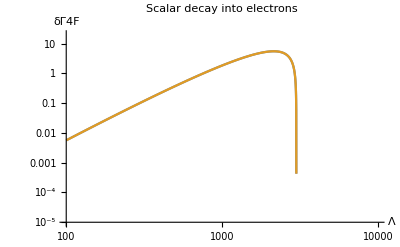

```mathematica
LogLogPlot[{-SWD[Mϕ,mtau,3000],-PWD[Mϕ,mtau,3000]},{Mϕ,10^2,10^4},PlotRange->{{10^2,10^4},{10^-5,20}},AxesLabel->{"Λ","δΓ4F"},PlotLabel->"Scalar decay into electrons"]
```

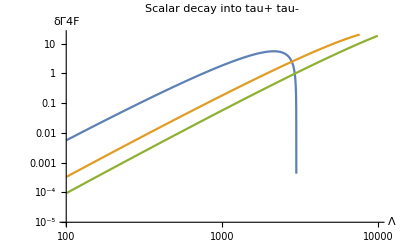

```mathematica
LogLogPlot[{-SWD[Mϕ,mtau,3000],-SWD[Mϕ,mtau,15000],-SWD[Mϕ,mtau,30000]},{Mϕ,10^2,10^4},PlotRange->{{10^2,10^4},{10^-5,20}},AxesLabel->{"Λ","δΓ4F"},PlotLabel->"Scalar decay into tau+ tau-"]
```

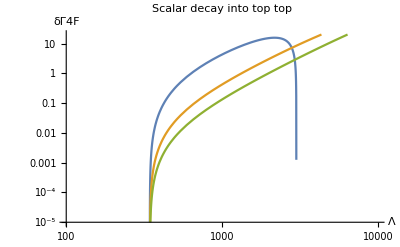

```mathematica
LogLogPlot[{-3*SWD[Mϕ,mtop,3000],-3*SWD[Mϕ,mtop,15000],-3*SWD[Mϕ,mtop,30000]},{Mϕ,10^2,10^4},PlotRange->{{10^2,10^4},{10^-5,20}},AxesLabel->{"Λ","δΓ4F"},PlotLabel->"Scalar decay into top top"]
```

```mathematica
Clear[Y,MH,MW,g]
```

# Higgs decay into 2 fermions

## Ancho de decaimiento

```mathematica
casoH:={Subscript[y, s]^f->((g*mf)/(2MW)),Mϕ->MH}
```

```mathematica
Hfinal=FullSimplify[final/.casoH]
```

(N √(1-(4 mf^2)/MH^2) (S^2 (MH^2-4 mf^2) y_s^(2 f)+MH^2 P^2 y_p^(2 f)))/(8 π MH)

```mathematica
HExpfin=FullSimplify[Normal[Series[Hfinal/.pert,{S,0,1},{P,0,1}]]/.{δS^2->0,δP^2->0}]
```

(N √(1-(4 mf^2)/MH^2) (δS S (MH^2-4 mf^2) y_s^(2 f)+δP MH^2 P y_p^(2 f)))/(4 π MH)

## Interaccion 4 fermiones

### canal S

```mathematica
HSC=Coefficient[Mvs,S*Subscript[y, s]^f]
```

(3 (2 mf^2-Mϕ^2) log(Λ^2/Mϕ^2))/(32 Λ^2)

### Canal t

```mathematica
HPC=Coefficient[Mvt/.casoH,P*Subscript[y, p]^f*dm[5]]
```

0

## Corrección ancho de decaimiento H->ff

```mathematica
HWD4FI=Simplify[Coefficient[HExpfin,S]/.{δS->HSC}] /.casoH/.{y->mf*2}(* SWD4FI = Scalar width decay due 4 fermions interaction *)
```

(3 N √(1-(4 mf^2)/MH^2) (2 mf^2-MH^2) (MH^2-4 mf^2) y_s^(2 f) log(Λ^2/MH^2))/(128 π Λ^2 MH)

```mathematica
PHWD4FI=Simplify[Coefficient[HExpfin,P]/.{δP->HPC}] (* SWD4FI = Scalar width decay due 4 fermions interaction *)
```

0

```mathematica
Comparision between Higgs and Z
```

```mathematica
yu=2.69;
yd=0.37
yl=0.37
g=0.6
MW=80
MZ=90
MH=125
Me=0.0005
Mμ=0.1
Mτ=1.77
Mu=0.002
Md=0.005
Mc=1.27
Ms=0.095
Mt=172.44
Mb=4.18
PWZe=83.98*10^-3
PWHe = 
FWZ=2.0
FWH=6.0*10^-3
Λ=10*10^3
```

2.69

0.37

0.37

0.6

80

90

125

0.0005

0.1

1.77

0.002

0.005

1.27

0.095

172.44

4.18

0.08398

2.

0.006

10000

```mathematica
Clear[MH]
```

```mathematica
DeltaZ=9.87*10^6*(1/Λ)^2*Log[Λ^2/MZ^2]
```

```mathematica
DeltaH=-3/512*(g^2*Me^2*MH)/(π*MW^2*Λ^2)(MH^2-2 Me^2)*(1-(4*Me^2)/MH^2)^(3/2)*Log[Λ^2/MH^2]
```

```mathematica
DeltaZ/FWZ
```

```mathematica
DeltaH/FWH
```

Partial Width

```mathematica
PWH[MH_,Mf_,y_,N_]:=(y^2*N*MH)/(8π)*(1-(4*Mf^2)/MH^2)^(3/2)
```

```mathematica
TWH[MH_]=PWH[MH,Me,yl,1]
```

0.00544708 (1-(1.×10^-6)/MH^2)^(3/2) MH

```mathematica
N[PWH[1,Me,yl,1]]
```

0.00544707